# Auger & EEL Spectroscopy

## Loading Stuffs I might need

```mathematica
<<ErrorBarPlots`
```

```mathematica
<<PhysicalConstants`
```

```mathematica
ClearSystemCache[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Helper Functions

### Reading in the data and doing stuff on it

This reads the data files from the Auger experiment, it’s two rows of data and the first 8 lines are pretty much useless comments

```mathematica
ClearAll[ReadRawData]
ReadRawData[filename_]:=Module[{file,data},
file=OpenRead[filename];
Skip[file,String,8];
data=ReadList[file,{Real,Real}];
Close[file];
Return[data]
]
```

```mathematica
ClearAll[AllDataFiles]
AllDataFiles[path_]:=FileNames["./data/"~~path~~"/*.dat"]
```

Selects data points in a certain x interval

```mathematica
ClearAll[TakeRegion]
TakeRegion[data_,min_,max_]:=Select[data,First[#]≥min&& First[#]≤max&]
```

```mathematica
ClearAll[Around]
Around[data_,value_]:=First[Nearest[First[dataᵀ],value]]
```

```mathematica
ClearAll[GaussPeakFit]
GaussPeakFit[data_,{min_,max_}]:=Module[{region,midpoint,maxheight},
region=Select[data,First[#]≥min&& First[#]≤max&];
midpoint=Round[(min+max)/2];
maxheight=Min[region⟦All,2⟧];
NonlinearModelFit[region,A*Exp[(-(x-a)^2)/b]+c,{{A,maxheight},{a,midpoint},b,c},x,MaxIterations->10000]
]
```

```mathematica
ClearAll[GaussDoublePeakFit]
GaussDoublePeakFit[data_,{min_,max_},maxheight1_,maxheight2_,midpoint1_,midpoint2_]:=Module[{region},
region=Select[data,First[#]≥min&& First[#]≤max&];
NonlinearModelFit[region,A1*Exp[(-(x-a1)^2)/b1]+A2*Exp[(-(x-a2)^2)/b2]+c,{{A1,maxheight1},{a1,midpoint1},{A2,maxheight2},{a2,midpoint2},b1,b2,c},x,MaxIterations->10000]
]
```

```mathematica
ClearAll[LorentzPeakFit]
LorentzPeakFit[data_,{min_,max_}]:=Module[{region,midpoint,maxheight},
region=Select[data,First[#]≥min&& First[#]≤max&];
midpoint=Round[(min+max)/2];
maxheight=Min[region⟦All,2⟧];
NonlinearModelFit[region,A/(1+(x-a)^2/b)+c,{{A,maxheight},{a,midpoint},b,c},x,MaxIterations->1000]
]
```

```mathematica
ClearAll[SpectrumIntegrate]
SpectrumIntegrate[data_]:=Module[{i,int},
int={{data⟦1,1⟧,0}};
For[i=2,i≤Length[data],i++,int=int~Join~{{data⟦i,1⟧,int⟦i-1,2⟧+(data⟦i,1⟧-data⟦i-1,1⟧)(data⟦i,2⟧+data⟦i-1,2⟧)/2}}];
int
];
```

### Plotting and shiny stuff

```mathematica
ClearAll[ErrorForm]
ErrorForm[{x_?NumberQ,Δx_?NumberQ},dgts_:2]:=ToString[PaddedForm[N[Round[x,10^(-dgts)]],{dgts+2,dgts}]]<>" ±"<>ToString[PaddedForm[N[Ceiling[Abs[Δx],10^(-dgts)]],{dgts+1,dgts}]]
```

```mathematica
niceStyle={
Axes->True,
Frame->True,
GridLines->Automatic,
ImageSize->600,
ImageMargins->3,
LabelStyle->{16,Bold},
FrameTicksStyle->{Directive[16,Plain],Directive[16,Plain]},
FrameStyle->Thick,
GridLinesStyle->Directive[Dashed,Gray],
AxesStyle->Directive[Dashed,Gray]
};
```

```mathematica
ClearAll[PeakFitPlot]
PeakFitPlot[data_, fit_, title_: "", bottom_: "", left_: ""] := Show[ListPlot[data, PlotLabel -> Style[title, 16], FrameLabel -> {StyleForm[bottom, FontSize -> 14], StyleForm[left, FontSize -> 14]}], Plot[Normal[fit], {x, Min[First[#] & /@ data], Max[First[#] & /@ data]}], niceStyle]
```

```mathematica
ClearAll[GroupPeakFitPlot]
GroupPeakFitPlot[data_, fits_, title_: "", bottom_: "", left_: ""] := Show[ListPlot[data, PlotLabel -> Style[title, 16], FrameLabel -> {StyleForm[bottom, FontSize -> 14], StyleForm[left, FontSize -> 14]}], Plot[Evaluate[Normal[#] & /@ fits], {x, Min[First[#] & /@ (Join @@ data)], Max[First[#] & /@ (Join @@ data)]}], niceStyle]
```

## Import Data

### Sample Cleaning data

```mathematica
AllDataFiles["calib"]//TableForm
```

./data/calib/calib01.dat
./data/calib/calib02.dat
./data/calib/calib03.dat
./data/calib/calib04.dat
./data/calib/calib05.dat
./data/calib/calib06.dat
./data/calib/calib07.dat
./data/calib/calib08.dat
./data/calib/calib09.dat
./data/calib/calib10.dat
./data/calib/calib11.dat
./data/calib/calib12.dat
./data/calib/calib12_uebersicht.dat

```mathematica
calib=ReadRawData[#]&/@AllDataFiles["calib"];
```

### Auger Spectrum

```mathematica
AllDataFiles["a1"]//TableForm
```

./data/a1/a1_100_1500_1_1.dat
./data/a1/a1_1300_1500_1_3.dat

```mathematica
a1data=ReadRawData[#]&/@AllDataFiles["a1"];
```

### Bulk Plasmons

```mathematica
AllDataFiles["a2"]//TableForm
```

./data/a2/a2_900_1100_1_3.dat
./data/a2/a2_uebersicht.dat

```mathematica
a2data=ReadRawData[#]&/@AllDataFiles["a2"];
```

### Surface Plasmons

```mathematica
AllDataFiles["a3"]//TableForm
```

./data/a3/a3_100_250_1_1.dat
./data/a3/a3_140_210_1_3.dat
./data/a3/a3_uebersicht.dat

```mathematica
a3data=ReadRawData[#]&/@AllDataFiles["a3"];
```

## Sample Cleaning

```mathematica
Manipulate[ListPlot[TakeRegion[calib⟦m⟧,150,600],PlotRange->All,FrameTicks->{{Automatic,Automatic},{Automatic,{{190,"Cl"},{284.9,"C"},{400.2,"N"},{530,"O"}}}},FrameLabel->{"Electron Energy E [eV]","dN/dE [arb. Units]"},Epilog->(Line[{{First[#],5000},#}]&/@(Select[calib⟦m⟧,First[#]==Around[calib⟦m⟧,190]||First[#]==Around[calib⟦m⟧,284.9]||First[#]==Around[calib⟦m⟧,400.2]||First[#]==Around[calib⟦m⟧,530.2]&])),PlotStyle->{Directive[Thick,Blue,PointSize->Medium]},niceStyle],{m,1,Length[calib],1}]
```

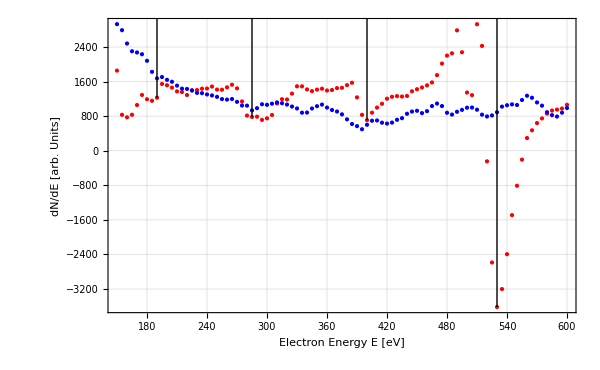

```mathematica
With[{m=2},ListPlot[{TakeRegion[calib⟦m⟧,150,600],TakeRegion[calib⟦12⟧,150,600]},PlotRange->All,FrameTicks->{{Automatic,Automatic},{Automatic,{{190,"Cl"},{284.9,"C"},{400.2,"N"},{530,"O"}}}},FrameLabel->{"Electron Energy E [eV]","dN/dE [arb. Units]"},Epilog->(Line[{{First[#],5000},#}]&/@(Select[calib⟦m⟧,First[#]==Around[calib⟦m⟧,190]||First[#]==Around[calib⟦m⟧,284.9]||First[#]==Around[calib⟦m⟧,400.2]||First[#]==Around[calib⟦m⟧,530.2]&])),PlotStyle->{Directive[Thick,Red,PointSize->Medium],Directive[Thick,Blue,PointSize->Medium]},niceStyle]]
```

## Auger Spectrum

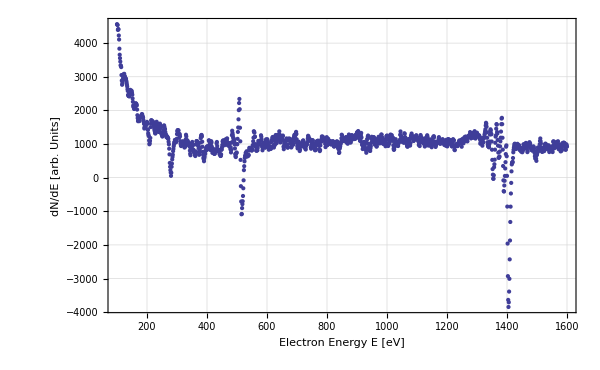

```mathematica
ListPlot[a1data⟦1⟧,PlotRange->All,FrameLabel->{"Electron Energy E [eV]","dN/dE [arb. Units]"},niceStyle]
```

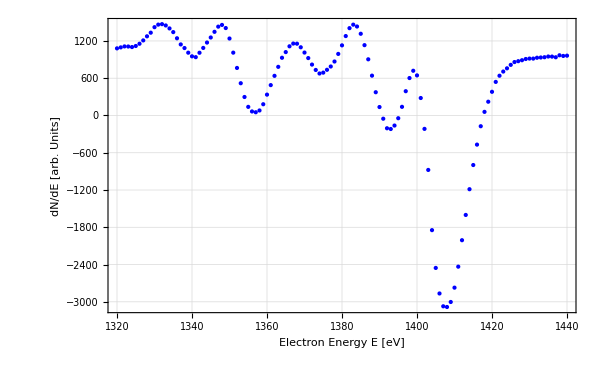

```mathematica
ListPlot[TakeRegion[a1data⟦2⟧,1320,1440],PlotRange->All,FrameLabel->{"Electron Energy E [eV]","dN/dE [arb. Units]"},PlotStyle->{Directive[Thick,Blue,PointSize->Medium]},niceStyle]
```

```mathematica
a1intervals={{1322,1338},{1335,1345},{1343,1352},{1352,1362},{1362,1372},{1372,1380},{1380,1388},{1388,1395},{1395,1403},{1400,1420}};
```

```mathematica
(*a1intervals={{1335,1345},{1352,1362},{1372,1380},{1388,1395},{1400,1420}};*)
```

```mathematica
a1fits=GaussPeakFit[a1data⟦2⟧,#]&/@a1intervals
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{FittedModel[1090.27+393.311 ⅇ^(-0.056388 (-«19»+x)^2)],FittedModel[1488.04-535.586 ⅇ^(-0.0415534 (-«19»+x)^2)],FittedModel[-9.9273×10^9+9.9273×10^9 ⅇ^(-2.60314×10^-9 (-«19»+x)^2)],FittedModel[2242.34-2197.77 ⅇ^(-0.0143701 (-«19»+x)^2)],FittedModel[-279.527+1432.75 ⅇ^(-0.0142646 (-«19»+x)^2)],FittedModel[2112.65-1426.43 ⅇ^(-0.0129497 (-«19»+x)^2)],FittedModel[-1357.27+2815.14 ⅇ^(-0.0139876 (-«19»+x)^2)],FittedModel[1894.09-2118.71 ⅇ^(-0.0216083 (-«19»+x)^2)],FittedModel[-2.50958×10^10+2.50958×10^10 ⅇ^(-2.90263×10^-9 (-«19»+x)^2)],FittedModel[588.656-3771.3 ⅇ^(-0.0273693 (-«19»+x)^2)]}

```mathematica
a1plotthis=Prepend[a1intervalsᵀ,a1fits]ᵀ;
```

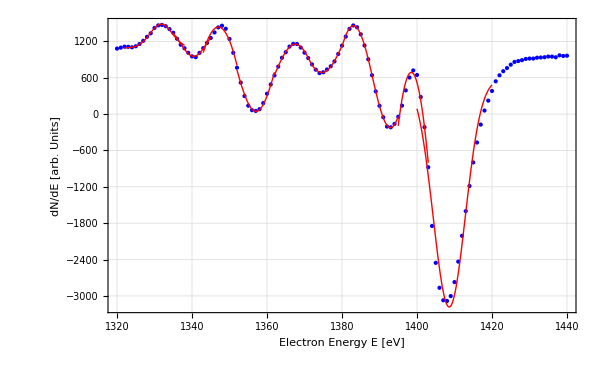

```mathematica
Show[ListPlot[TakeRegion[a1data⟦2⟧,1320,1440],PlotRange->All,FrameLabel->{"Electron Energy E [eV]","dN/dE [arb. Units]"},PlotStyle->{Directive[Thick,Blue,PointSize->Medium]},niceStyle],Show[(Plot[Normal[#⟦1⟧],{x,#⟦2⟧,#⟦3⟧},PlotRange->All,PlotStyle->Red]&/@a1plotthis)]]
```

```mathematica
#["ParameterTable"]&/@a1fits
```

{ | Estimate | Standard Error | t-Statistic | P-Value
A | 393.311 | 15.1549 | 25.9526 | 1.38843×10^-12
a | 1331.79 | 0.0995473 | 13378.5 | 8.58971×10^-48
b | 17.7343 | 1.89019 | 9.38227 | 3.75092×10^-7
c | 1090.27 | 12.8906 | 84.5788 | 3.29666×10^-19, | Estimate | Standard Error | t-Statistic | P-Value
A | -535.586 | 72.1595 | -7.42225 | 0.000146626
a | 1340.45 | 0.0612409 | 21888.1 | 1.09729×10^-28
b | 24.0654 | 5.59616 | 4.30034 | 0.0035651
c | 1488.04 | 75.9937 | 19.5811 | 2.26188×10^-7, | Estimate | Standard Error | t-Statistic | P-Value
A | 9.9273×10^9 | 800430. | 12402.5 | 1.85464×10^-23
a | 1347.04 | 0.145006 | 9289.55 | 1.05035×10^-22
b | 3.84151×10^8 | 4.13691×10^7 | 9.28593 | 0.0000882263
c | -9.9273×10^9 | 800408. | -12402.8 | 1.85433×10^-23, | Estimate | Standard Error | t-Statistic | P-Value
A | -2197.77 | 1695.34 | -1.29636 | 0.235951
a | 1357.08 | 0.0691758 | 19617.8 | 2.36165×10^-28
b | 69.5888 | 64.4345 | 1.07999 | 0.315945
c | 2242.34 | 1707.43 | 1.31329 | 0.230494, | Estimate | Standard Error | t-Statistic | P-Value
A | 1432.75 | 555.239 | 2.58042 | 0.0364503
a | 1367.54 | 0.048092 | 28435.9 | 1.75672×10^-29
b | 70.1035 | 32.9602 | 2.12691 | 0.070993
c | -279.527 | 559.726 | -0.4994 | 0.632809, | Estimate | Standard Error | t-Statistic | P-Value
A | -1426.43 | 708.87 | -2.01226 | 0.100356
a | 1374.66 | 0.0753017 | 18255.4 | 9.36159×10^-21
b | 77.2218 | 45.7622 | 1.68746 | 0.152319
c | 2112.65 | 713.159 | 2.96238 | 0.0314324, | Estimate | Standard Error | t-Statistic | P-Value
A | 2815.14 | 792.558 | 3.55197 | 0.0163532
a | 1383.05 | 0.0306192 | 45169.5 | 1.00943×10^-22
b | 71.4917 | 23.47 | 3.04609 | 0.0285514
c | -1357.27 | 796.646 | -1.70373 | 0.149158, | Estimate | Standard Error | t-Statistic | P-Value
A | -2118.71 | 387.011 | -5.47455 | 0.00541803
a | 1392.93 | 0.0432388 | 32214.8 | 5.57098×10^-18
b | 46.2785 | 11.0495 | 4.18831 | 0.0138254
c | 1894.09 | 391.706 | 4.83549 | 0.00842761, | Estimate | Standard Error | t-Statistic | P-Value
A | 2.50958×10^10 | 239308. | 104868. | 1.49655×10^-24
a | 1398.48 | 0.126272 | 11075.1 | 1.1391×10^-19
b | 3.44515×10^8 | 3.48608×10^7 | 9.88257 | 0.000180906
c | -2.50958×10^10 | 239261. | -104889. | 1.49508×10^-24, | Estimate | Standard Error | t-Statistic | P-Value
A | -3771.3 | 226.747 | -16.6322 | 5.94859×10^-12
a | 1408.59 | 0.168154 | 8376.81 | 1.11381×10^-57
b | 36.5373 | 6.03112 | 6.05813 | 0.0000127905
c | 588.656 | 231.129 | 2.54687 | 0.0208436}

```mathematica
{((a/.(#["BestFitParameters"]&/@a1fits))),(#["ParameterErrors"]⟦2⟧&/@a1fits)}ᵀ//TableForm
```

1331.79 | 0.0995473
1340.45 | 0.0612409
1347.04 | 0.145006
1357.08 | 0.0691758
1367.54 | 0.048092
1374.66 | 0.0753017
1383.05 | 0.0306192
1392.93 | 0.0432388
1398.48 | 0.126272
1408.59 | 0.168154

```mathematica
MovingAverage[((a/.(#["BestFitParameters"]&/@a1fits))),2]⟦1;;9;;2⟧//TableForm
```

1336.12
1352.06
1371.1
1387.99
1403.53

```mathematica
{((a/.(#["BestFitParameters"]&/@a1fits))-12.59),(#["ParameterErrors"]⟦2⟧&/@a1fits)}ᵀ//TableForm
```

1319.2 | 0.0995473
1327.86 | 0.0612409
1334.45 | 0.145006
1344.49 | 0.0691758
1354.95 | 0.048092
1362.07 | 0.0753017
1370.46 | 0.0306192
1380.34 | 0.0432388
1385.89 | 0.126272
1396. | 0.168154

```mathematica
MovingAverage[((a/.(#["BestFitParameters"]&/@a1fits))-12.59),2]⟦1;;9;;2⟧//TableForm
```

1323.53
1339.47
1358.51
1375.4
1390.94

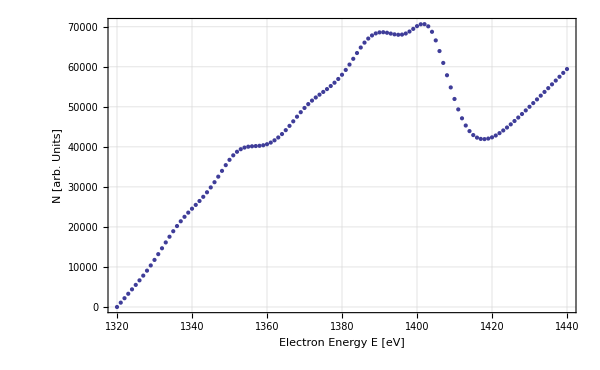

```mathematica
ListPlot[SpectrumIntegrate[TakeRegion[a1data⟦2⟧,1320,1440]],PlotRange->All,FrameLabel->{"Electron Energy E [eV]","N [arb. Units]"},niceStyle]
```

## Bulk Plasmons

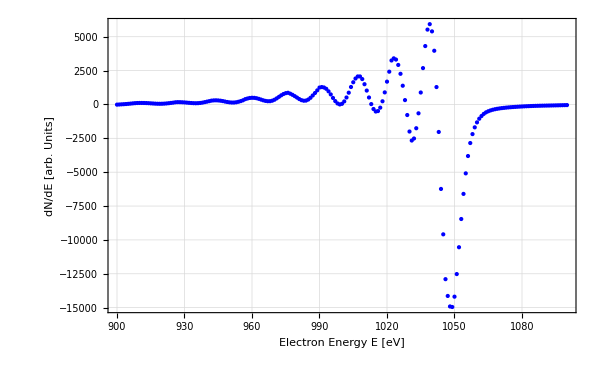

```mathematica
ListPlot[a2data⟦1⟧,PlotRange->All,FrameLabel->{"Electron Energy E [eV]","dN/dE [arb. Units]"},PlotStyle->{Directive[Thick,Blue,PointSize->Medium]},niceStyle]
```

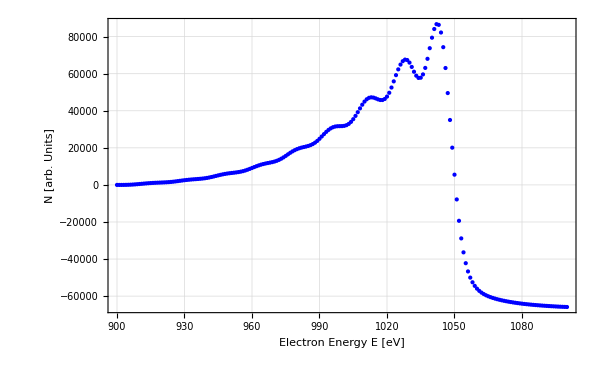

```mathematica
ListPlot[SpectrumIntegrate[a2data⟦1⟧],PlotRange->All,FrameLabel->{"Electron Energy E [eV]","N [arb. Units]"},PlotStyle->{Directive[Thick,Blue,PointSize->Medium]},niceStyle]
```

```mathematica
a2intervals={{990,1000},{1005,1018},{1022,1032},{1037,1045}};
```

```mathematica
a2fits=GaussPeakFit[SpectrumIntegrate[a2data⟦1⟧],#]&/@a2intervals
```

{FittedModel[-2211.64+34023.2 ⅇ^(-0.00307289 (-«18»+x)^2)],FittedModel[-38840.9+86144.1 ⅇ^(-0.00181031 (-«18»+x)^2)],FittedModel[39206.+28409.9 ⅇ^(-0.019226 (-«19»+x)^2)],FittedModel[57906.6+29156.4 ⅇ^(-0.0636182 (-«18»+x)^2)]}

```mathematica
a2plotthis=Prepend[a2intervalsᵀ,a2fits]ᵀ;
```

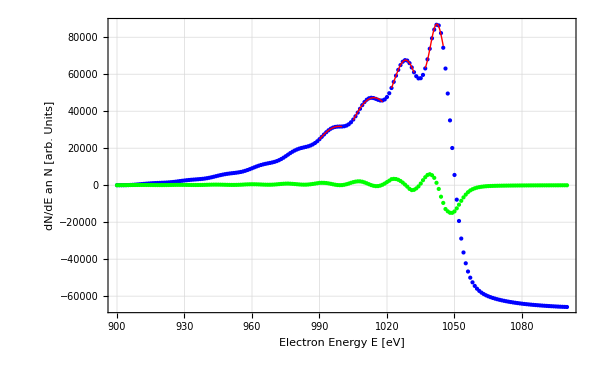

```mathematica
Show[ListPlot[SpectrumIntegrate[a2data⟦1⟧],PlotRange->All,FrameLabel->{"Electron Energy E [eV]","dN/dE an N [arb. Units]"},PlotStyle->{Directive[Thick,Blue,PointSize->Medium]},niceStyle],ListPlot[a2data⟦1⟧,PlotRange->All,PlotStyle->{Directive[Thick,Green,PointSize->Medium]}],Show[(Plot[Normal[#⟦1⟧],{x,#⟦2⟧,#⟦3⟧},PlotRange->All,PlotStyle->Red]&/@a2plotthis)]]
```

```mathematica
#["ParameterTable"]&/@a2fits
```

{ | Estimate | Standard Error | t-Statistic | P-Value
A | 34023.2 | 16241.1 | 2.09488 | 0.0744313
a | 998.655 | 0.167131 | 5975.29 | 9.71094×10^-25
b | 325.426 | 181.685 | 1.79116 | 0.11638
c | -2211.64 | 16253.6 | -0.136071 | 0.895595, | Estimate | Standard Error | t-Statistic | P-Value
A | 86144.1 | 138869. | 0.620327 | 0.548918
a | 1014.17 | 0.191439 | 5297.62 | 1.41349×10^-33
b | 552.393 | 960.384 | 0.575179 | 0.577882
c | -38840.9 | 138998. | -0.279434 | 0.785606, | Estimate | Standard Error | t-Statistic | P-Value
A | 28409.9 | 1028.4 | 27.6254 | 2.09062×10^-8
a | 1028.27 | 0.0122388 | 84016.8 | 8.93745×10^-33
b | 52.0128 | 2.62365 | 19.8246 | 2.07721×10^-7
c | 39206. | 1050.68 | 37.3149 | 2.58119×10^-9, | Estimate | Standard Error | t-Statistic | P-Value
A | 29156.4 | 2179.94 | 13.3749 | 0.0000418006
a | 1042.15 | 0.0579764 | 17975.5 | 1.01135×10^-20
b | 15.7188 | 2.38658 | 6.58633 | 0.00121168
c | 57906.6 | 2337.3 | 24.775 | 1.9984×10^-6}

```mathematica
plasmonpos=NonlinearModelFit[{Table[i,{i,1,4}],Take[(a/.(#["BestFitParameters"]&/@a2fits)),4]}ᵀ,m*x+n,{m,n},x,
Weights->Take[(#["ParameterErrors"]⟦2⟧&/@a2fits)^-2,4],
VarianceEstimatorFunction->(1&)]
```

FittedModel[985.688+14.1872 x]

```mathematica
plasmonpos["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
m | 14.1872 | 0.0465047 | 305.071 | 0.0000107446
n | 985.688 | 0.14133 | 6974.35 | 2.05586×10^-8

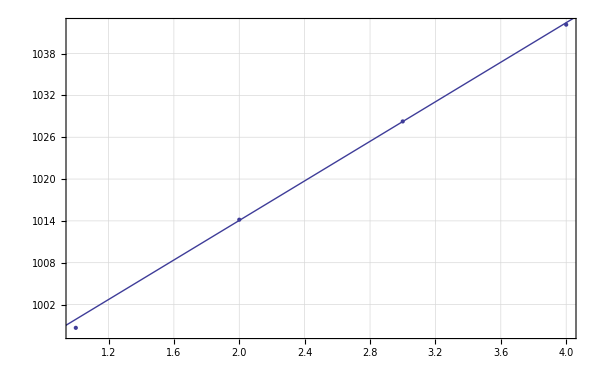

```mathematica
Show[ErrorListPlot[{Table[i,{i,1,4}],a/.(#["BestFitParameters"]&/@a2fits),#["ParameterErrors"]⟦2⟧&/@a2fits}ᵀ],Plot[Normal[plasmonpos],{x,0.5,4.5}],niceStyle]
```

## Surface Plasmons

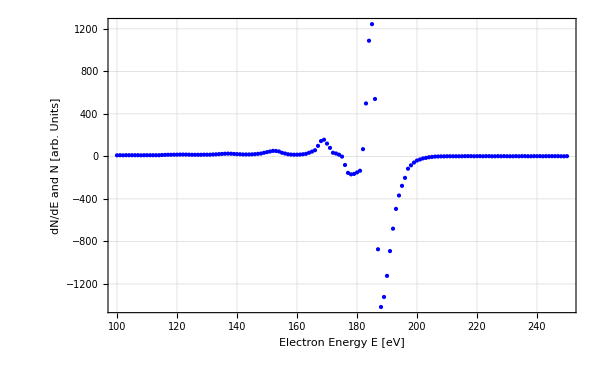

```mathematica
ListPlot[a3data⟦1⟧,PlotRange->All,FrameLabel->{"Electron Energy E [eV]","dN/dE and N [arb. Units]"},PlotStyle->{Directive[Thick,Blue,PointSize->Medium]},niceStyle]
```

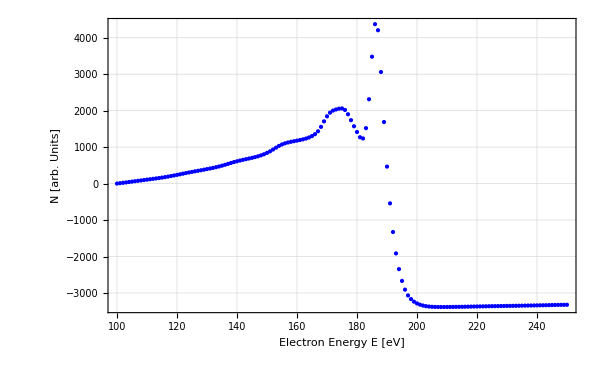

```mathematica
ListPlot[SpectrumIntegrate[a3data⟦1⟧],PlotRange->All,FrameLabel->{"Electron Energy E [eV]","N [arb. Units]"},PlotStyle->{Directive[Thick,Blue,PointSize->Medium]},niceStyle]
```

```mathematica
a3intervals={{182,190}};
```

```mathematica
a3fits=GaussPeakFit[SpectrumIntegrate[a3data⟦1⟧],#]&/@a3intervals
```

{FittedModel[678.328+3782.96 ⅇ^(-0.16767 (-«19»+x)^2)]}

```mathematica
a3plotthis=Prepend[a3intervalsᵀ,a3fits]ᵀ;
```

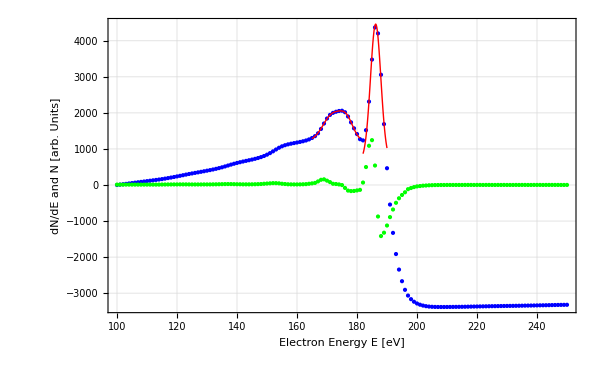

```mathematica
Show[ListPlot[SpectrumIntegrate[a3data⟦1⟧],PlotRange->All,FrameLabel->{"Electron Energy E [eV]","dN/dE and N [arb. Units]"},PlotStyle->{Directive[Thick,Blue,PointSize->Medium]},niceStyle],Plot[Normal[surfacebulk],{x,165,181},PlotRange->All,PlotStyle->Red],ListPlot[a3data⟦1⟧,PlotRange->All,PlotStyle->{Directive[Thick,Green,PointSize->Medium]}],Show[(Plot[Normal[#⟦1⟧],{x,#⟦2⟧,#⟦3⟧},PlotRange->All,PlotStyle->Red]&/@a3plotthis)]]
```

```mathematica
#["ParameterTable"]&/@a3fits
```

{ | Estimate | Standard Error | t-Statistic | P-Value
A | 3782.96 | 388.192 | 9.74508 | 0.000193458
a | 186.224 | 0.121525 | 1532.4 | 2.24618×10^-15
b | 5.96409 | 1.77387 | 3.3622 | 0.0200597
c | 678.328 | 398.374 | 1.70274 | 0.149347}

```mathematica
surfacebulk=GaussDoublePeakFit[SpectrumIntegrate[a3data⟦1⟧],{165,181},1900,2100,171,176]
```

FittedModel[1209.01+481.884 ⅇ^(-0.101729 («1»)^2)+743.224 ⅇ^(-0.0469139 (-«19»+x)^2)]

```mathematica
surfacebulk["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
A1 | 743.224 | 48.0263 | 15.4754 | 2.58965×10^-8
a1 | 171.953 | 0.404238 | 425.377 | 1.26839×10^-22
A2 | 481.884 | 96.3497 | 5.00141 | 0.000536215
a2 | 176.667 | 0.24604 | 718.041 | 6.75415×10^-25
b1 | 21.3156 | 3.56373 | 5.98127 | 0.000135454
b2 | 9.83 | 1.35661 | 7.24601 | 0.0000277151
c | 1209.01 | 23.5566 | 51.3237 | 1.90711×10^-13

## Playarea

evendumberfit=NonlinearModelFit[TakeRegion[a1data⟦2⟧,1325,1420],A1*Exp[(-(x-a1)^2)/b1]+A2*Exp[(-(x-a2)^2)/b2]+A3*Exp[(-(x-a3)^2)/b3]+A4*Exp[(-(x-a4)^2)/b4]+A5*Exp[(-(x-a5)^2)/b5]+A6*Exp[(-(x-a6)^2)/b6]+Aa*Exp[(-(x-aa)^2)/ba]+Ab*Exp[(-(x-ab)^2)/bb]+Ac*Exp[(-(x-ac)^2)/bc]+Ad*Exp[(-(x-ad)^2)/bd]+Ae*Exp[(-(x-ae)^2)/be]+c,{{A1,1000},{A2,1000},{A3,0},{A4,600},{A5,-250},{A6,-3200},{Aa,1400},{Ab,1400},{Ac,1200},{Ad,1400},{Ae,600},{a1,1325},{a2,1340},{a3,1356},{a4,1375},{a5,1394},{a6,1408},{aa,1347},{ab,1408},{ac,1366},{ad,1383},{ae,1398},b1,b2,b3,b4,b5,b6,ba,bb,bc,bd,be,c},x,MaxIterations→1000000]

NonlinearModelFit::cvmit: "Failed to converge to the requested accuracy or precision within 1000000 iterations. "

FittedModel[177.441+«12»+«19» «1»-104834. ⅇ^(-0.0174306 «1»)]

evendumberfit1[{"ParameterTable", "RSquared"}]

{"" | "Estimate" | "Standard Error" | "t-Statistic" | "P-Value"
A1 | -56947.7 | 1.5485×10^7 | -0.00367761 | 0.997077
A2 | -4878.39 | 84068.8 | -0.0580285 | 0.953907
A3 | 60442.5 | 1.54975×10^7 | 0.00390014 | 0.9969
A4 | 919.885 | 242.588 | 3.79196 | 0.000333565
A5 | -1938.78 | 12392. | -0.156454 | 0.876168
A6 | -56693.7 | 3.87309×10^7 | -0.00146378 | 0.998837
Aa | 965.404 | 832.109 | 1.16019 | 0.250281
Ab | 53494.9 | 3.8731×10^7 | 0.00138119 | 0.998902
Ac | 357.237 | 590.691 | 0.604778 | 0.547465
Ad | 1990.06 | 8526.69 | 0.233391 | 0.816202
Ae | 774.361 | 2517.4 | 0.307603 | 0.759383
a1 | 1331.29 | 55.0962 | 24.163 | 7.07192×10^-34
a2 | 1337.34 | 9.81823 | 136.21 | 1.44006×10^-80
a3 | 1331.69 | 48.5599 | 27.4236 | 4.33602×10^-37
a4 | 1368.3 | 1.94994 | 701.714 | 4.35402×10^-126
a5 | 1391.21 | 4.50836 | 308.584 | 2.92304×10^-103
a6 | 1408.54 | 10.5825 | 133.101 | 6.28016×10^-80
aa | 1348.74 | 0.710989 | 1896.99 | 9.96682×10^-154
ab | 1408.57 | 10.6927 | 131.732 | 1.21421×10^-79
ac | 1363.53 | 1.22319 | 1114.74 | 5.95898×10^-139
ad | 1387.39 | 30.8721 | 44.9398 | 3.97676×10^-50
ae | 1400.33 | 1.22872 | 1139.66 | 1.44739×10^-139
b1 | 70.2047 | 736.59 | 0.0953103 | 0.924366
b2 | 42.1229 | 151.287 | 0.27843 | 0.78158
b3 | 75.8655 | 761.039 | 0.0996867 | 0.920905
b4 | 25.6275 | 18.4479 | 1.38919 | 0.169591
b5 | 37.4097 | 98.4066 | 0.380155 | 0.705089
b6 | 20.9821 | 293.976 | 0.0713734 | 0.943323
ba | 14.8602 | 8.0521 | 1.8455 | 0.069591
bb | 20.1446 | 295.103 | 0.068263 | 0.945789
bc | 10.1235 | 10.9791 | 0.922071 | 0.359955
bd | 89.8005 | 233.349 | 0.384834 | 0.701637
be | 13.9338 | 27.2404 | 0.511511 | 0.610753
c | 142.196 | 78.3846 | 1.81408 | 0.074353,0.998486}

Show[ListPlot[TakeRegion[a1data[[2]], 1320, 1440], PlotRange -> All, FrameLabel -> {"Electron Energy E [eV]", "dN/dE [arb. Units]"}, PlotStyle -> {Directive[Thick, Blue, PointSize -> Medium]}, niceStyle], Plot[Normal[evendumberfit1], {x, 1325, 1420}, PlotStyle -> Red]]

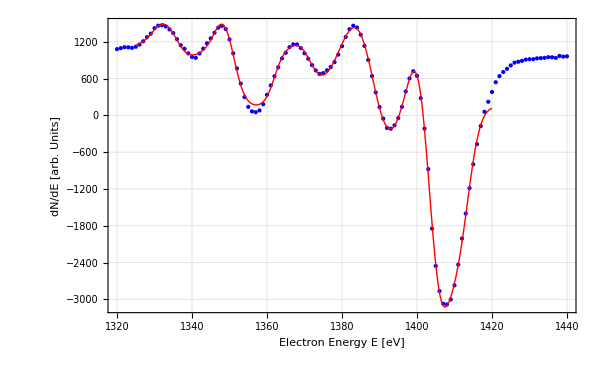

evendumberfit1=NonlinearModelFit[TakeRegion[a1data⟦2⟧,1323,1420],A1*Exp[(-(x-a1)^2)/b1]+A2*Exp[(-(x-a2)^2)/b2]+A3*Exp[(-(x-a3)^2)/b3]+A4*Exp[(-(x-a4)^2)/b4]+A5*Exp[(-(x-a5)^2)/b5]+A6*Exp[(-(x-a6)^2)/b6]+Aa*Exp[(-(x-aa)^2)/ba]+Ab*Exp[(-(x-ab)^2)/bb]+Ac*Exp[(-(x-ac)^2)/bc]+Ad*Exp[(-(x-ad)^2)/bd]+Ae*Exp[(-(x-ae)^2)/be]+c,{{A1,1000},{A2,1000},{A3,0},{A4,600},{A5,-250},{A6,-3200},{Aa,1400},{Ab,1400},{Ac,1200},{Ad,1400},{Ae,600},{a1,1325},{a2,1340},{a3,1356},{a4,1375},{a5,1394},{a6,1408},{aa,1347},{ab,1408},{ac,1366},{ad,1383},{ae,1398},b1,b2,b3,b4,b5,b6,ba,bb,bc,bd,be,c},x,MaxIterations→100000]

NonlinearModelFit::cvmit: "Failed to converge to the requested accuracy or precision within 100000 iterations. "

FittedModel[142.196+«12»+«18» ⅇ^(«1»)-56947.7 ⅇ^(-0.0142441 «1»)]

dumbfit=NonlinearModelFit[TakeRegion[a1data⟦2⟧,1323,1420],A1*Exp[(-(x-a1)^2)/b1]+A2*Exp[(-(x-a2)^2)/b2]+A3*Exp[(-(x-a3)^2)/b3]+A4*Exp[(-(x-a4)^2)/b4]+A5*Exp[(-(x-a5)^2)/b5]+A6*Exp[(-(x-a6)^2)/b6]+Aa*Exp[(-(x-aa)^2)/ba]+Ab*Exp[(-(x-ab)^2)/bb]+Ac*Exp[(-(x-ac)^2)/bc]+Ad*Exp[(-(x-ad)^2)/bd]+Ae*Exp[(-(x-ae)^2)/be]+c,{{A1,1000},{A2,1000},{A3,0},{A4,600},{A5,-250},{A6,-3200},{Aa,1400},{Ab,1400},{Ac,1200},{Ad,1400},{Ae,600},{a1,1325},{a2,1340},{a3,1356},{a4,1375},{a5,1394},{a6,1408},{aa,1347},{ab,1408},{ac,1366},{ad,1383},{ae,1398},b1,b2,b3,b4,b5,b6,ba,bb,bc,bd,be,c},x,MaxIterations→100000]

NonlinearModelFit::cvmit: "Failed to converge to the requested accuracy or precision within 100000 iterations. "

FittedModel[142.196+«12»+«18» ⅇ^(«1»)-56947.7 ⅇ^(-0.0142441 «1»)]

dumbfit[{"ParameterTable", "RSquared"}]

{"" | "Estimate" | "Standard Error" | "t-Statistic" | "P-Value"
A1 | -56947.7 | 1.5485×10^7 | -0.00367761 | 0.997077
A2 | -4878.39 | 84068.8 | -0.0580285 | 0.953907
A3 | 60442.5 | 1.54975×10^7 | 0.00390014 | 0.9969
A4 | 919.885 | 242.588 | 3.79196 | 0.000333565
A5 | -1938.78 | 12392. | -0.156454 | 0.876168
A6 | -56693.7 | 3.87309×10^7 | -0.00146378 | 0.998837
Aa | 965.404 | 832.109 | 1.16019 | 0.250281
Ab | 53494.9 | 3.8731×10^7 | 0.00138119 | 0.998902
Ac | 357.237 | 590.691 | 0.604778 | 0.547465
Ad | 1990.06 | 8526.69 | 0.233391 | 0.816202
Ae | 774.361 | 2517.4 | 0.307603 | 0.759383
a1 | 1331.29 | 55.0962 | 24.163 | 7.07192×10^-34
a2 | 1337.34 | 9.81823 | 136.21 | 1.44006×10^-80
a3 | 1331.69 | 48.5599 | 27.4236 | 4.33602×10^-37
a4 | 1368.3 | 1.94994 | 701.714 | 4.35402×10^-126
a5 | 1391.21 | 4.50836 | 308.584 | 2.92304×10^-103
a6 | 1408.54 | 10.5825 | 133.101 | 6.28016×10^-80
aa | 1348.74 | 0.710989 | 1896.99 | 9.96682×10^-154
ab | 1408.57 | 10.6927 | 131.732 | 1.21421×10^-79
ac | 1363.53 | 1.22319 | 1114.74 | 5.95898×10^-139
ad | 1387.39 | 30.8721 | 44.9398 | 3.97676×10^-50
ae | 1400.33 | 1.22872 | 1139.66 | 1.44739×10^-139
b1 | 70.2047 | 736.59 | 0.0953103 | 0.924366
b2 | 42.1229 | 151.287 | 0.27843 | 0.78158
b3 | 75.8655 | 761.039 | 0.0996867 | 0.920905
b4 | 25.6275 | 18.4479 | 1.38919 | 0.169591
b5 | 37.4097 | 98.4066 | 0.380155 | 0.705089
b6 | 20.9821 | 293.976 | 0.0713734 | 0.943323
ba | 14.8602 | 8.0521 | 1.8455 | 0.069591
bb | 20.1446 | 295.103 | 0.068263 | 0.945789
bc | 10.1235 | 10.9791 | 0.922071 | 0.359955
bd | 89.8005 | 233.349 | 0.384834 | 0.701637
be | 13.9338 | 27.2404 | 0.511511 | 0.610753
c | 142.196 | 78.3846 | 1.81408 | 0.074353,0.998486}

Show[ListPlot[TakeRegion[a1data[[2]], 1320, 1440], PlotRange -> All, FrameLabel -> {"Electron Energy E [eV]", "dN/dE [arb. Units]"}, PlotStyle -> {Directive[Thick, Blue, PointSize -> Medium]}, niceStyle], Plot[Normal[dumbfit], {x, 1323, 1420}, PlotStyle -> Red]]

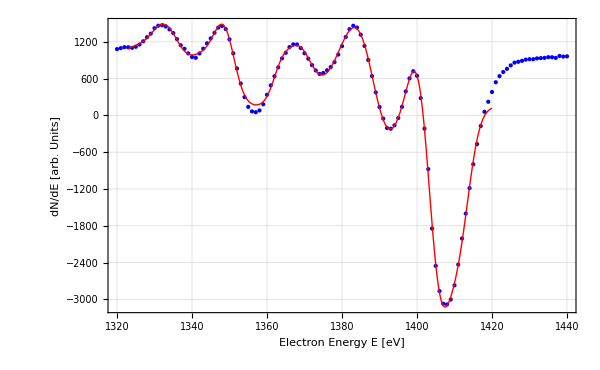

FindMaximum[Normal[dumbfit], {x, 1340}]

{1487.7, {x -> 1332.28}}

FindMaximum[Normal[dumbfit], {x, 1345}]

{1486.64, {x -> 1347.89}}

FindMaximum[Normal[dumbfit], {x, 1360}]

{1430.62, {x -> 1383.24}}

FindMaximum[Normal[dumbfit], {x, 1360}]